```mathematica
(*FIND THE NUMBER OF OCCURRENCES OF {0,1,1,0,1} IN EACH STEP OF CellularAutomaton[30,{{1},0},100] USING ListLinePlot TO DISPLAY THE RESULT*)
```

```mathematica
pom=CellularAutomaton[30,{{1},0},100]
```

{«1»}

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},100]]
```

-Graphics-

```mathematica
smallpom= CellularAutomaton[30,{{1},0},10]
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,1,1,1,1,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0},{0,0,1,1,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0},{0,1,1,0,1,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0},{1,1,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,0,0,1}}

```mathematica
smallpomred=smallpom //.{x___,0,1,1,0,1,y___}->{x,Red,Red,Red,Red,Red,y}
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],1,1,1,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],1,1,1,0,0,1,1,1,1,1,1,0,0,0},{0,0,1,1,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0},{RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[1,0,0],1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0},{1,1,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,0,0,1}}

```mathematica
(*in questo conto un certo elemento in ogni riga*)
```

```mathematica
Count[#,1]& /@ smallpom
```

{1,3,3,6,4,9,5,12,7,12,11}

```mathematica
smallpomchanged=smallpom //.{x___,0,1,1,0,1,y___}->{x,2,y}
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,1,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,2,1,1,1,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,2,1,1,1,0,0,1,1,1,1,1,1,0,0,0},{0,0,1,1,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0},{2,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,0},{1,1,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,0,0,1}}

```mathematica
Count[#,2]& /@ smallpomchanged
```

{0,0,0,1,0,1,0,1,0,1,0}

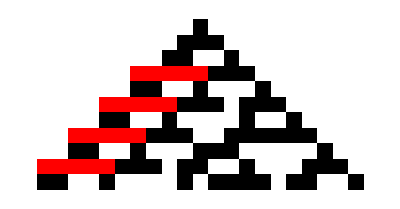

```mathematica
ArrayPlot[smallpomred]
```

```mathematica
pomchanged=pom//.{x___,0,1,1,0,1,y___}->{x,2,y}
```

{«1»}

```mathematica
r=Count[#,2,{1}]& /@ pomchanged
```

{0,0,0,1,0,1,0,1,0,1,0,2,1,2,0,2,0,1,1,2,0,1,2,3,1,2,2,4,1,3,1,3,0,4,1,5,0,2,3,3,2,3,1,4,2,3,2,5,1,3,2,7,0,4,3,6,2,3,5,5,0,6,5,3,2,5,4,4,3,6,7,3,0,6,5,5,6,6,5,6,3,5,3,9,3,7,10,6,1,7,6,7,2,8,6,5,3,5,8,5,3}

```mathematica
pomred=pom//.{x___,0,1,1,0,1,y___}->{x,Red,Red,Red,Red,Red,y}
```

{«1»}

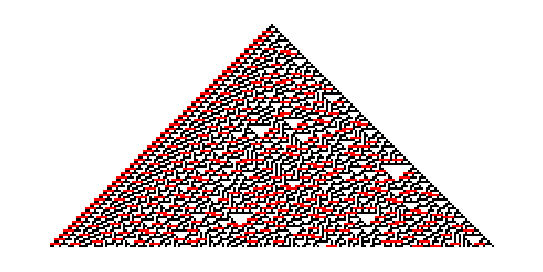

```mathematica
ArrayPlot[pomred]
```

```mathematica
(*notes*)
```

```mathematica
{1,1,3,2,1,1,4}/.{x___,1,1,y___}->{x,a,y}
```

{a,3,2,1,1,4}

```mathematica
{1,1,3,2,1,1,4}//.{x___,1,1,y___}->{x,a,y}
```

{a,3,2,a,4}

```mathematica
(*la regola di sostituzione /. per contare mi sembrava buona, ma sostituisce una volta sola a riga -> QUINDI BISOGNA USARE REPLACE REPEATED che è questa //. *)
```

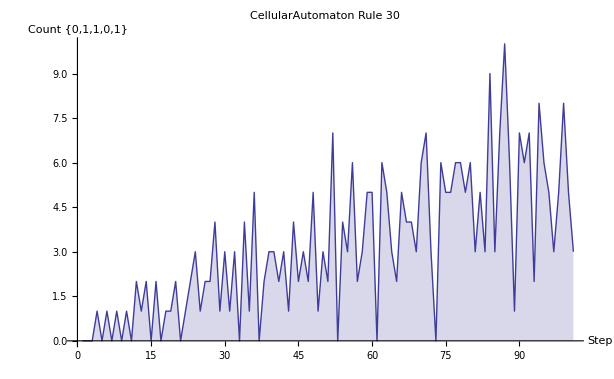

```mathematica
ListLinePlot[r, Filling->Axis, AxesLabel-> {"Step","Count {0,1,1,0,1}"},PlotLabel->"CellularAutomaton Rule 30"]
```